```mathematica
$Line = 0;
```

```mathematica
(* 
Define LP:;
	max z = 0x1 + 4x2 + 2;
	g1 = -x1 - 2x2 ≥ -2;
	g2 = -2x1 + x2 ≤ 1;
	g3 = x1 - 3x2 ≤ 5;
	g4 = -3x1 - 2x2 ≥ 3
*)
m0 ={y1,y2,y3,y4,1,""};
m1={-1,1,-2,2,2,s1};
m2={2,-2,-1,1,1,s2};
m3={-1,1,3,-3,5,s3};
m4={-3,3,-2,2,-3,s4};
mobj={0,0,-4,4,-2,-z->min};
t0={m0,m1,m2,m3,m4,mobj};
```

```mathematica
(* Pivoting as a Function *)
pivot[iStar_, jStar_, m_] := (
(* Create copy of matrix  and get dimensions *)
mm = m;
rows = Dimensions[m][[1]];
cols = Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]= m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]= -m[[row,col]]/m[[iStar, jStar]]],

If[row≠iStar && col== jStar,
mm[[row,col]]= m[[row,col]]/m[[iStar, jStar]]],

If[row≠iStar && col ≠ jStar,
mm[[row,col]]= m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

```mathematica
t1 = pivot[4,3,t0];
Print["t0 = ", MatrixForm[t0]]
Print["t1 = ", MatrixForm[t1]]
```

t1 = (y1 | y2 | s3 | y4 | 1 | 
-5/3 | 5/3 | -2/3 | 0 | 16/3 | s1
5/3 | -5/3 | -1/3 | 0 | 8/3 | s2
1/3 | -1/3 | 1/3 | 1 | -5/3 | y3
-11/3 | 11/3 | -2/3 | 0 | 1/3 | s4
-4/3 | 4/3 | -4/3 | 0 | 14/3 | -z→min)

t0 = (y1 | y2 | y3 | y4 | 1 | 
-1 | 1 | -2 | 2 | 2 | s1
2 | -2 | -1 | 1 | 1 | s2
-1 | 1 | 3 | -3 | 5 | s3
-3 | 3 | -2 | 2 | -3 | s4
0 | 0 | -4 | 4 | -2 | -z→min)

```mathematica
Max[(336/13)/(-15/13),(102/13)/(-28/13),(64/13)/(-1/13)]
(* The Max test can be substitued for a Min test because we attempt to find the largest absolute value out of a set of negative numbers.

Therefore, the above max funciton becomes: *)
Min[336/15, 102/28, 64/1]
```

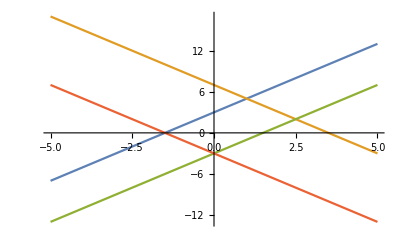

```mathematica
myPlot = Plot[{y=2x+3, y=-2x+7,y=2x-3, y=-2x-3},{x,-5,5}]
```

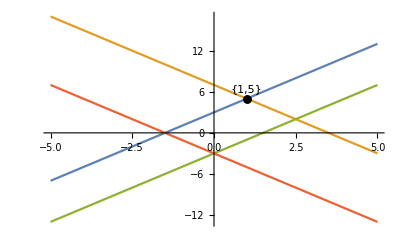

```mathematica
pt1 = {1,5};
epiPoints = {};
epiPoints=Union[epiPoints,{Text[pt1, Offset[{0,10},pt1]]}];
myPlot2=Show[myPlot, Graphics[{PointSize[0.016], Point[pt1]}], Epilog->epiPoints]
```

{Text[{1,5},Offset[{0,10},{1,5}]],Text[{2.5,2},Offset[{0,10},{2.5,2}]]}

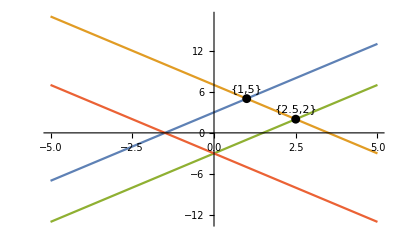

```mathematica
pt2 = {2.5,2};
epiPoints=Union[epiPoints,{Text[pt2, Offset[{0,10},pt2]]}]
myPlot3=Show[myPlot2, Graphics[{PointSize[0.016], Point[pt2]}], Epilog->epiPoints]
```